```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/2.1/2.1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/2.1/~$2.1.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/2.1/2.1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset1

```mathematica
dataset1=makeDataset[raw⟦4⟧]
```

Dataset[<>]

```mathematica
data1 =raw⟦4⟧⟦2;;⟧;
```

```mathematica
func1 = Interpolation[data1,InterpolationOrder->2]
```

InterpolatingFunction[…]

## Dataset2

```mathematica
dataset2 = makeDataset[raw⟦5⟧]
```

Dataset[<>]

```mathematica
data2 =raw⟦5⟧⟦2;;⟧;
Max[data2]
```

79.32

```mathematica
func2 = Interpolation[data2,InterpolationOrder->2]
```

InterpolatingFunction[…]

## Dataset3

```mathematica
dataset3 = makeDataset[raw⟦6⟧]
```

Dataset[<>]

```mathematica
data3 = raw⟦6⟧⟦2;;⟧;
```

```mathematica
func3 = Interpolation[data3,InterpolationOrder->2]
```

InterpolatingFunction[…]

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

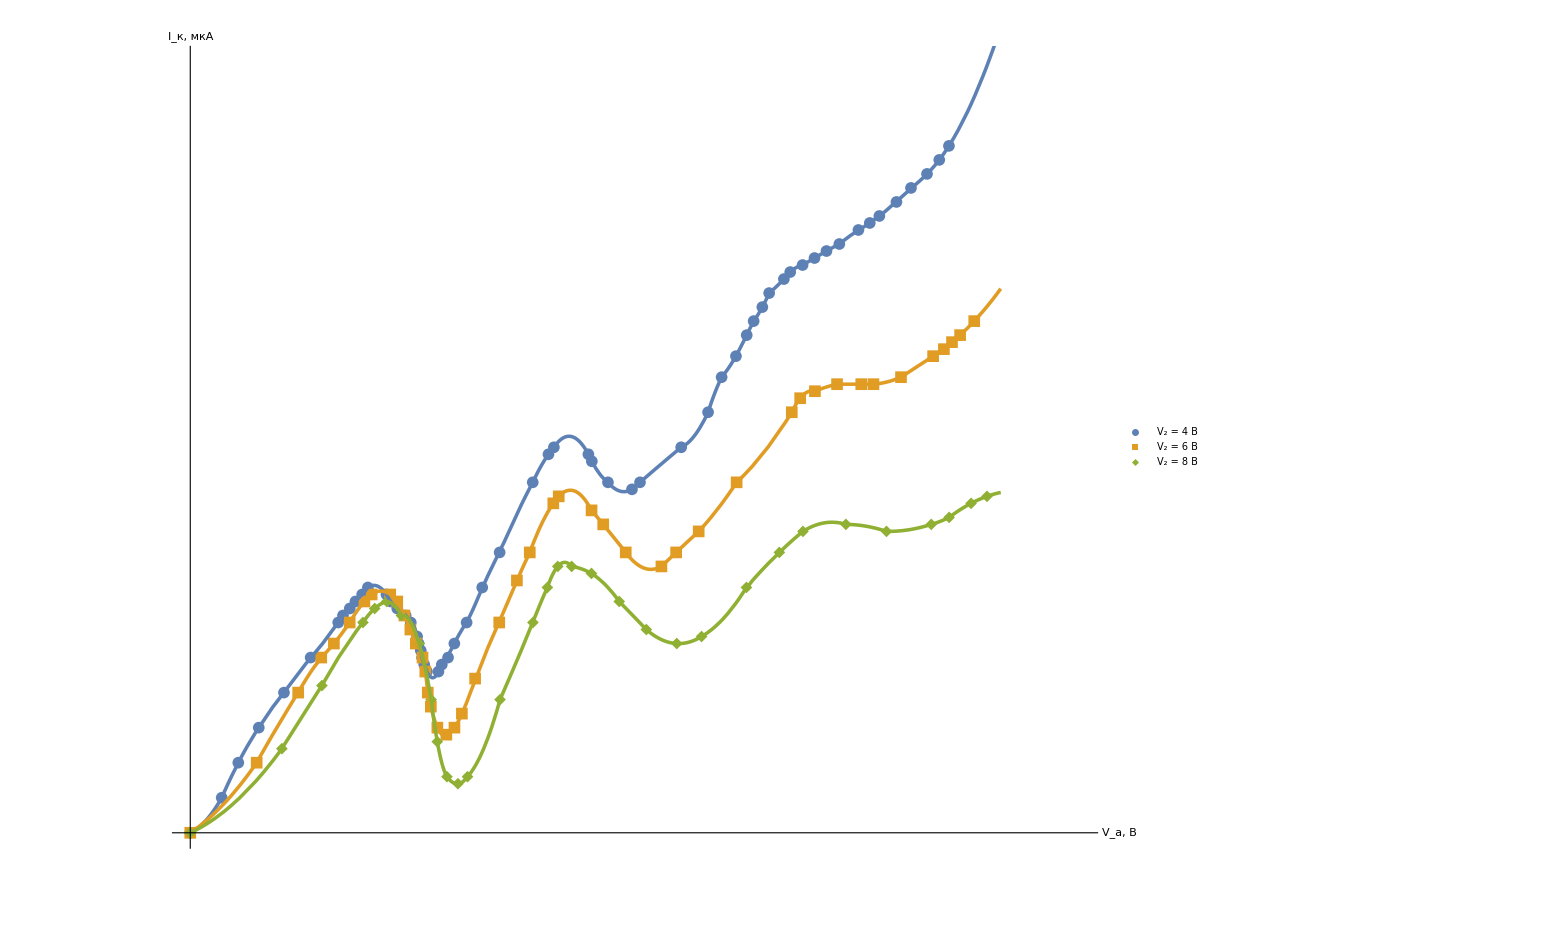

```mathematica
Show[
ListPlot[
{dataset1,dataset2,dataset3},
PlotRange-> {{0,90},{0, 110}},
Ticks-> {Range[-1000,1000, 5],Range[-1000,1000, 5]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["V_(:0430), В", Large], Style["I_(:043a), мкA", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 1],Range[-1000,1000, 2.5]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
Automatic,
{"V_2 = 4 В","V_2 = 6 В", "V_2 = 8 В"},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.2],Scaled[0.75]}
]
],
Plot[{func1[x],func2[x],func3[x]},{x,0,82},
PlotStyle->{Thickness->0.0017}
]


]
```

## data1

```mathematica
FindMaximum[{func1[x],x < 20},{x,0}]
```

{35.2983,{x→18.5792}}

```mathematica
FindMinimum[{func1[x],x>20,x < 30},{x,0}]
```

{22.1198,{x→24.525}}

```mathematica
FindMaximum[{func1[x],x >33, x<40},{x,0}]
```

{56.5691,{x→38.321}}

```mathematica
FindMinimum[{func1[x],x>40,x < 45},{x,0}]
```

{48.6667,{x→43.88}}

## data2

```mathematica
FindMaximum[{func2[x],x < 22},{x,0}]
```

{34.4805,{x→19.29}}

```mathematica
FindMinimum[{func2[x],x>23,x < 26},{x,0}]
```

{13.908,{x→25.7053}}

```mathematica
FindMaximum[{func2[x],x >37, x<40},{x,0}]
```

{48.8686,{x→38.4584}}

```mathematica
FindMinimum[{func2[x],x >44, x<65},{x,0}]
```

{37.5822,{x→46.61}}

## data3

```mathematica
FindMaximum[{func3[x],x < 24},{x,0}]
```

{31.0197,{x→21.477}}

```mathematica
FindMinimum[{func3[x],x>25,x < 30},{x,0}]
```

{6.99545,{x→27.01}}

```mathematica
FindMaximum[{func3[x],x >35, x<40},{x,0}]
```

{38.5773,{x→37.885}}

```mathematica
FindMinimum[{func3[x],x >44, x<65},{x,0}]
```

{37.5822,{x→46.61}}